```mathematica
(*
Вариант 1: 
f(x) = 2^x, [-2,1]
*)
(*
1. Постройте интерполяционные многочлены степени n для функции f(x),
заданной в равноотстоящих точках отрезка[a,b] (согласно номера вашего варианта),
и исследуйте зависимость погрешности интерполирования от
степени полинома n (n=1,2,3,4,5 и 10) (или, что равносильно,
от расстояния между узлами h=(b-a)/n).Для этого:
а) создайте таблицу значений заданной функции в равноотстоящих точках отрезка 
xj = a+(b-a)/n*j, j=0,1,...,n и выведите в виде списка и таблицы;
*)
a=  -2;
b = 1;
f[x_]:=2^x;
n=1;
j=0;
xs1 = {};
fxs1 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs1 = Append[xs1,xj];
fxs1 = Append[fxs1,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs1,fxs1}];

TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | 1 | 2

```mathematica
n=2;
j=0;
xs2 = {};
fxs2 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs2 = Append[xs2,xj];
fxs2 = Append[fxs2,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs2,fxs2}];

TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | -1/2 | 1/(√2)
2 | 1 | 2

```mathematica
n=3;
j=0;
xs3 = {};
fxs3 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs3 = Append[xs3,xj];
fxs3 = Append[fxs3,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs3,fxs3}];

TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | -1 | 1/2
2 | 0 | 1
3 | 1 | 2

```mathematica
n=4;
j=0;
xs4 = {};
fxs4 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs4 = Append[xs4,xj];
fxs4 = Append[fxs4,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs4,fxs4}];

TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | -5/4 | 1/(2 2^(1/4))
2 | -1/2 | 1/(√2)
3 | 1/4 | 2^(1/4)
4 | 1 | 2

```mathematica
n=5;
j=0;
xs5 = {};
fxs5 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs5 = Append[xs5,xj];
fxs5 = Append[fxs5,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs5,fxs5}];
TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | -7/5 | 1/(2 2^(2/5))
2 | -4/5 | 1/2^(4/5)
3 | -1/5 | 1/2^(1/5)
4 | 2/5 | 2^(2/5)
5 | 1 | 2

```mathematica
n=10;
j=0;
xs10 = {};
fxs10 = {};
While[j<=n,
xj=a+(b-a)/n*j;
xs10 = Append[xs10,xj];
fxs10 = Append[fxs10,f[xj]];
j=j+1;
];
js=Range[0,n];
data=Transpose[{js,xs10,fxs10}];

TableForm[data,TableHeadings->{None,{"j","xj","f(xj)"}}]
```

j | xj | f(xj)
0 | -2 | 1/4
1 | -17/10 | 1/(2 2^(7/10))
2 | -7/5 | 1/(2 2^(2/5))
3 | -11/10 | 1/(2 2^(1/10))
4 | -4/5 | 1/2^(4/5)
5 | -1/2 | 1/(√2)
6 | -1/5 | 1/2^(1/5)
7 | 1/10 | 2^(1/10)
8 | 2/5 | 2^(2/5)
9 | 7/10 | 2^(7/10)
10 | 1 | 2

```mathematica
(*
б) найдите интерполяционный многочлен N(X) n с помощью встроенной функции 
InterpolatingPolinomial и выведите его,упростите вид полученного 
многочлена при помощи функции Expand или Collect;
*)
data1=Transpose[{xs1,fxs1}]
P1 = InterpolatingPolynomial[data1,x]
```

{{-1/2+3/(2 √2),2^(-1/2+3/(2 √2))},{-1/2-3/(2 √2),2^(-1/2-3/(2 √2))}}

2^(-1/2+3/(2 √2))-1/3 √2 (2^(-1/2-3/(2 √2))-2^(-1/2+3/(2 √2))) (1/2-3/(2 √2)+x)

```mathematica
data2=Transpose[{xs2,fxs2}]
P2 = Expand[N[InterpolatingPolynomial[data2,x]]]
```

{{-1/2+(3 √3)/4,2^(-1/2+(3 √3)/4)},{-1/2,1/(√2)},{-1/2-(3 √3)/4,2^(-1/2-(3 √3)/4)}}

1.03207+0.740753 x+0.181657 x^2

```mathematica
data3=Transpose[{N[xs3],N[fxs3]}]
P3 = Expand[N[InterpolatingPolynomial[data3,x]]]
```

{{0.885819,1.84781},{0.0740251,1.05265},{-1.07403,0.474992},{-1.88582,0.27059}}

0.998996+0.706238 x+0.247784 x^2+0.0414171 x^3

```mathematica
data4=Transpose[{N[xs4],N[fxs4]}]
P4 = Expand[N[InterpolatingPolynomial[data4,x]]]
```

{{0.926585,1.90077},{0.381678,1.30286},{-0.5,0.707107},{-1.38168,0.383772},{-1.92658,0.263051}}

0.999514+0.693311 x+0.243312 x^2+0.056195 x^3+0.00711336 x^4

```mathematica
data5=Transpose[{N[xs5],N[fxs5]}]
P5 = Expand[N[InterpolatingPolynomial[data5,x]]]
```

{{-2.,0.25},{-1.4,0.378929},{-0.8,0.574349},{-0.2,0.870551},{0.4,1.31951},{1.,2.}}

0.999979+0.693061 x+0.240417 x^2+0.0559707 x^3+0.00959496 x^4+0.000977368 x^5

```mathematica
data10=Transpose[{N[xs10],N[fxs10]}]
P10 = Expand[N[InterpolatingPolynomial[data10,x]]]
```

{{0.984732,1.97895},{0.864448,1.82064},{0.633624,1.55146},{0.310961,1.24053},{-0.0774012,0.947763},{-0.5,0.707107},{-0.922599,0.527558},{-1.31096,0.403052},{-1.63362,0.322278},{-1.86445,0.274628},{-1.98473,0.25266}}

1.+0.693147 x+0.240227 x^2+0.0555041 x^3+0.00961813 x^4+0.00133335 x^5+0.000154036 x^6+0.0000152597 x^7+1.32434×10^-6 x^8+9.94492×10^-8 x^9+5.1021×10^-9 x^10

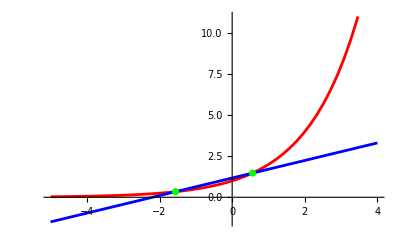

```mathematica
(*
в) выведите графики функции f(x),узлов интерполирования и 
интерполяционного многочлена N(x) n на отрезке[a-h,b+h];
*)
n=1;
h= (b-a)/n;
xmin = a-h;
xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P1,{x,xmin,xmax},PlotStyle->Blue];
p31=ListPlot[data1,PlotStyle->Green];
Show[p1,p2,p31,PlotRange->All]
```

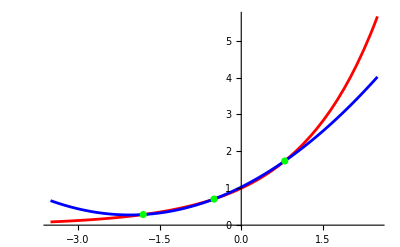

```mathematica
n=2;
h= (b-a)/n;
xmin = a-h;
xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P2,{x,xmin,xmax},PlotStyle->Blue];
p32=ListPlot[data2,PlotStyle->Green];
Show[p1,p2,p32,PlotRange->All]
```

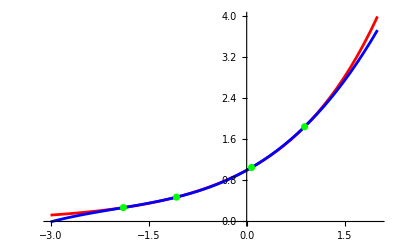

```mathematica
n=3;
h= (b-a)/n;
xmin = a-h;
xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P3,{x,xmin,xmax},PlotStyle->Blue];
p33=ListPlot[data3,PlotStyle->Green];
Show[p1,p2,p33,PlotRange->All]
```

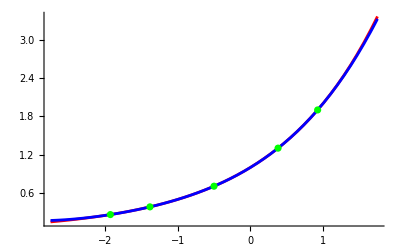

```mathematica
n=4;
h= (b-a)/n;
xmin = a-h;
xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P4,{x,xmin,xmax},PlotStyle->Blue];
p34=ListPlot[data4,PlotStyle->Green];
Show[p1,p2,p34,PlotRange->All]
```

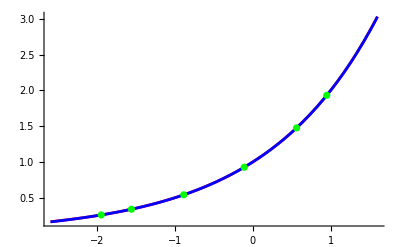

```mathematica
n=5;
h= (b-a)/n;
xmin = a-h;
xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P5,{x,xmin,xmax},PlotStyle->Blue];
p35=ListPlot[data5,PlotStyle->Green];
Show[p1,p2,p35,PlotRange->All]
```

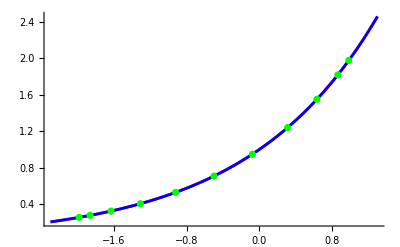

```mathematica
n=10;
h= (b-a)/n;
xmin = a-h;

xmax = b+h;
p1=Plot[f[x],{x,xmin,xmax}, PlotStyle->Red];
p2=Plot[P10,{x,xmin,xmax},PlotStyle->Blue];
p310=ListPlot[data10,PlotStyle->Green];
Show[p1,p2,p310,PlotRange->All]
```

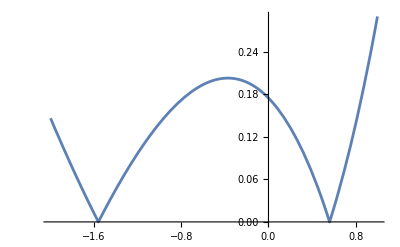

```mathematica
Rn1 = Plot[Abs[f[x]-P1],{x,a,b},PlotRange->All]
```

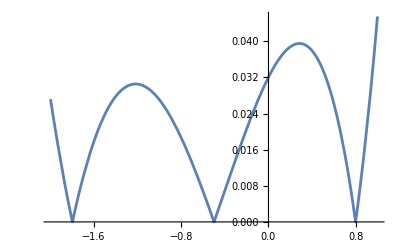

```mathematica
Rn2 = Plot[Abs[f[x]-P2],{x,a,b},PlotRange->All]
```

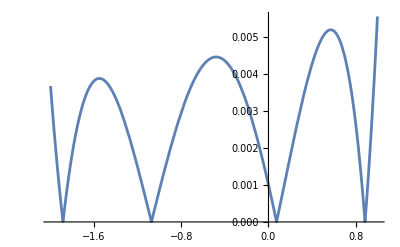

```mathematica
Rn3 = Plot[Abs[f[x]-P3],{x,a,b},PlotRange->All]
```

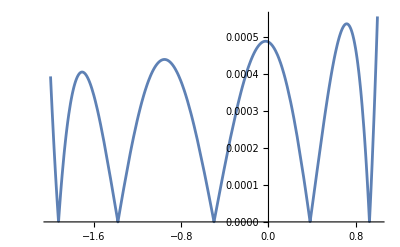

```mathematica
Rn4 = Plot[Abs[f[x]-P4],{x,a,b},PlotRange->All]
```

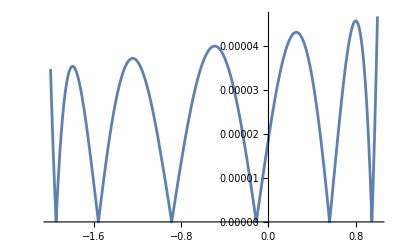

```mathematica
Rn5 = Plot[Abs[f[x]-P5],{x,a,b},PlotRange->All]
```

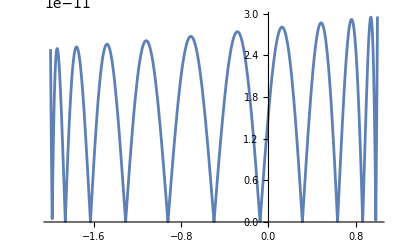

```mathematica
Rn10 = Plot[Abs[f[x]-P10],{x,a,b},PlotRange->All]
```

```mathematica
FindMaximum[{Abs[f[x]-P1],a<=x<=b},x]
```

{0.289793,{x→1.}}

```mathematica
FindMaximum[{Abs[f[x]-P2],a<=x<=b},x]
```

{0.0395289,{x→0.28392}}

```mathematica
FindMaximum[{Abs[f[x]-P3],a<=x<=b},x]
```

{0.00520315,{x→0.571158}}

```mathematica
FindMaximum[{Abs[f[x]-P4],a<=x<=b},x]
```

{0.000535053,{x→0.717419}}

```mathematica
FindMaximum[{Abs[f[x]-P5],a<=x<=b},x]
```

{0.0000465681,{x→0.99992}}

```mathematica
FindMaximum[{Abs[f[x]-P10],a<=x<=b},x]
```

{2.84107×10^-11,{x→0.468745}}

```mathematica
(*
2. Повторите п.1 для неравноотстоящих узлов на отрезке[a,b]–узлы 
расположить пропорционально нулям многочленов Чебышева:
xk = (a+b)/2+(b-a)/2 * cos((2k+1)*pi/(2(n+1))), k=0,1,...,n
*)
n=1;
k=0;
xs1 = {};
fxs1 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs1 = Append[xs1,xk];
fxs1 = Append[fxs1,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs1,fxs1}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+3/(2 √2) | 2^(-1/2+3/(2 √2))
1 | -1/2-3/(2 √2) | 2^(-1/2-3/(2 √2))

```mathematica
n=2;
k=0;
xs2 = {};
fxs2 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs2 = Append[xs2,xk];
fxs2 = Append[fxs2,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs2,fxs2}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+(3 √3)/4 | 2^(-1/2+(3 √3)/4)
1 | -1/2 | 1/(√2)
2 | -1/2-(3 √3)/4 | 2^(-1/2-(3 √3)/4)

```mathematica
n=3;
k=0;
xs3 = {};
fxs3 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs3 = Append[xs3,xk];
fxs3 = Append[fxs3,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs3,fxs3}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+3/2 Cos[π/8] | 2^(-1/2+3/2 Cos[π/8])
1 | -1/2+3/2 Sin[π/8] | 2^(-1/2+3/2 Sin[π/8])
2 | -1/2-3/2 Sin[π/8] | 2^(-1/2-3/2 Sin[π/8])
3 | -1/2-3/2 Cos[π/8] | 2^(-1/2-3/2 Cos[π/8])

```mathematica
n=4;
k=0;
xs4 = {};
fxs4 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs4 = Append[xs4,xk];
fxs4 = Append[fxs4,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs4,fxs4}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+3/2 √(5/8+(√5)/8) | 2^(-1/2+3/2 √(5/8+(√5)/8))
1 | -1/2+3/2 √(5/8-(√5)/8) | 2^(-1/2+3/2 √(5/8-(√5)/8))
2 | -1/2 | 1/(√2)
3 | -1/2-3/2 √(5/8-(√5)/8) | 2^(-1/2-3/2 √(5/8-(√5)/8))
4 | -1/2-3/2 √(5/8+(√5)/8) | 2^(-1/2-3/2 √(5/8+(√5)/8))

```mathematica
n=5;
k=0;
xs5 = {};
fxs5 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs5 = Append[xs5,xk];
fxs5 = Append[fxs5,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs5,fxs5}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+(3 (1+√3))/(4 √2) | 2^(-1/2+(3 (1+√3))/(4 √2))
1 | -1/2+3/(2 √2) | 2^(-1/2+3/(2 √2))
2 | -1/2+(3 (-1+√3))/(4 √2) | 2^(-1/2+(3 (-1+√3))/(4 √2))
3 | -1/2-(3 (-1+√3))/(4 √2) | 2^(-1/2-(3 (-1+√3))/(4 √2))
4 | -1/2-3/(2 √2) | 2^(-1/2-3/(2 √2))
5 | -1/2-(3 (1+√3))/(4 √2) | 2^(-1/2-(3 (1+√3))/(4 √2))

```mathematica
n=10;
k=0;
xs10 = {};
fxs10 = {};
While[k<=n,
xk=(a+b)/2+(b-a)/2*Cos[(2k+1)*Pi/(2(n+1))];
xs10 = Append[xs10,xk];
fxs10 = Append[fxs10,f[xk]];
k=k+1;
];
ks=Range[0,n];
data=Transpose[{ks,xs10,fxs10}];

TableForm[data,TableHeadings->{None,{"j","xk","f(xk)"}}]
```

j | xk | f(xk)
0 | -1/2+3/2 Cos[π/22] | 2^(-1/2+3/2 Cos[π/22])
1 | -1/2+3/2 Cos[(3 π)/22] | 2^(-1/2+3/2 Cos[(3 π)/22])
2 | -1/2+3/2 Cos[(5 π)/22] | 2^(-1/2+3/2 Cos[(5 π)/22])
3 | -1/2+3/2 Sin[(2 π)/11] | 2^(-1/2+3/2 Sin[(2 π)/11])
4 | -1/2+3/2 Sin[π/11] | 2^(-1/2+3/2 Sin[π/11])
5 | -1/2 | 1/(√2)
6 | -1/2-3/2 Sin[π/11] | 2^(-1/2-3/2 Sin[π/11])
7 | -1/2-3/2 Sin[(2 π)/11] | 2^(-1/2-3/2 Sin[(2 π)/11])
8 | -1/2-3/2 Cos[(5 π)/22] | 2^(-1/2-3/2 Cos[(5 π)/22])
9 | -1/2-3/2 Cos[(3 π)/22] | 2^(-1/2-3/2 Cos[(3 π)/22])
10 | -1/2-3/2 Cos[π/22] | 2^(-1/2-3/2 Cos[π/22])

```mathematica
(*
3. Выполните интерполяцию функции f (x) сплайном Sf (x) с помощью
функции Interpolation[data,Method->“Spline”),используя таблицу 
значений функции f (x) в равноотстоящих точках для n=5 и 10:
*)
data5=Transpose[{N[xs5],N[fxs5]}]
P5 = Interpolation[data5,Method->"Spline"]
```

{{-2.,0.25},{-1.4,0.378929},{-0.8,0.574349},{-0.2,0.870551},{0.4,1.31951},{1.,2.}}

InterpolatingFunction[…]

```mathematica
data10=Transpose[{N[xs10],N[fxs10]}]
P10 = Interpolation[data10,Method->"Spline"]
```

{{-2.,0.25},{-1.7,0.307786},{-1.4,0.378929},{-1.1,0.466516},{-0.8,0.574349},{-0.5,0.707107},{-0.2,0.870551},{0.1,1.07177},{0.4,1.31951},{0.7,1.6245},{1.,2.}}

InterpolatingFunction[…]